# Graviton Basis Toolkit User Guide

This notebook is the notebook and PDF rendering of graviton_basis_toolkit_user_guide.md. It is the short practical guide for normal use.

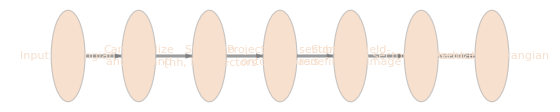

## Load the Toolkit

```mathematica
Get["graviton_basis_toolkit.wl"]
```

## Compute Sector Data

```mathematica
res = RunBasisComputation[
  "MaxDimension" -> 5,
  "CacheDirectory" -> FileNameJoin[{Directory[], "basis_cache"}],
  "UseCache" -> True,
  "Verbose" -> True
];
```

Once res exists you can inspect individual sectors.

```mathematica
RawBasisOfSector[res, 3, 2]
IBPBasisOfSector[res, 3, 2]
PhysicalBasisOfSector[res, 3, 2]
RedefinitionRulesOfSector[res, 3, 2]
```

## Reduce a Single Sector

```mathematica
red = ReduceSectorLagrangian[lag32, 3, 2,
  "CacheDirectory" -> FileNameJoin[{Directory[], "basis_cache"}],
  "UseCache" -> True
];

red["ReducedExpression"]
red["PhysicalCoordinates"]
```

## Reduce a General Lagrangian

```mathematica
red = ReduceLagrangian[lag,
  "CacheDirectory" -> FileNameJoin[{Directory[], "basis_cache"}],
  "UseCache" -> True
];

red["ReducedExpression"]
Keys[red["SectorReductions"]]
```

## How to Read the Counts

RawCount: size of the canonicalized raw spanning set.

IBPCount: dimension after quotienting by total derivatives.

RedefRank: rank of the field-redefinition image inside the IBP basis.

PhysicalCount: final count after removing that image.

Quadratic sectors are only reduced modulo IBP; interaction sectors are reduced modulo IBP and field redefinitions.

## Reproducible Validation

```mathematica
& 'C:\Program Files\Wolfram Research\Wolfram\14.2\WolframKernel.exe' -script graviton_basis_toolkit_validation.wls
```

The validation output is written to graviton_basis_toolkit_validation_output.wl and summarized in the validation report notebook and PDF.

## Common Pitfalls

Use the same h, eta, and PD symbols defined by the toolkit.

Do not interpret PhysicalCount as a gauge-invariant count unless you have separately imposed gauge invariance.

If the basis-generation logic changes, clear or replace the cache directory before trusting old cache files.